## solution data

```mathematica
M3 = Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/heated_cavity/result_M3.txt","Table"];
```

```mathematica
M13 = Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/heated_cavity/result_M13.txt","Table"];
```

```mathematica
dvmSol = Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/DVM/heated_cavity/result_DVM_10.txt","Table"];
```

```mathematica
GetQ[data_]:=Module[{qx,qy},

qx = Table[{{data⟦1,ii⟧,data⟦2,ii⟧},data⟦-2,ii⟧},{ii,1,Length[data⟦1⟧]}];
qy = Table[{{data⟦1,ii⟧,data⟦2,ii⟧},data⟦-1,ii⟧},{ii,1,Length[data⟦1⟧]}];

qx = Interpolation[qx];
qy = Interpolation[qy];

{qx,qy}
]
```

## Plot heat streamlines

```mathematica
CompareStreamLines[momSol_,dvmSol_,Mvalue_]:=Module[{},

Show[{StreamPlot[{momSol⟦1⟧[x,y],momSol⟦2⟧[x,y]},{x,0,1},{y,0,1},StreamPoints->{Automatic,0.1},ImageSize->Large,StreamStyle->Green,PlotLegends->Style[StringJoin["M=",ToString[Mvalue]],FontSize->14],Frame->True,FrameTicksStyle->16],StreamPlot[{dvmSol⟦1⟧[x,y],dvmSol⟦2⟧[x,y]},{x,0,1},{y,0,1},StreamStyle->Blue,StreamPoints->{Automatic,0.1},ImageSize->Large,PlotLegends->"DVM",Frame->True,FrameTicksStyle->16]}]
]
```

```mathematica
qM3 = GetQ[M3];
qM13 = GetQ[M13];
qDVM = GetQ[dvmSol];
```

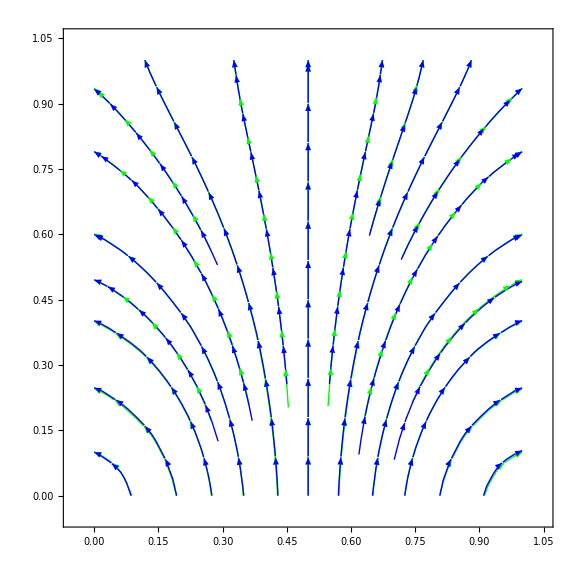

```mathematica
CompareStreamLines[qM13,qDVM,3]
```

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},StreamColorFunction->Function[{x,y,vx,vy,n},ColorData["AvocadoColors"][x y]]]
```